## Prep

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/leima/GitHub/WhyMathematica/misc

```mathematica
imgSize=700;
```

The purpose of this is not only to demonstrate how to do iteration as usual but also to demonstrate the idea that we can traslate itration idea to something else.

## Iteration

可以实现循环的（部分）

Do, For, Table, Map, MapThread, Scan
Fold, FoldList
Nest, NestList
Module

尽量不使用 Do, For 这类循环。另外，Do 比 For 快。例如,

```mathematica
t=x;Do[t=1/(1+t),{5}];t
```

1/(1+1/(1+1/(1+1/(1+1/(1+x)))))

Can be translated to

## Example

### Monte Carlo

The idea is that we DO NOT iterate but generate a list or table first.

#### Calculate Pi Directly

http://reference.wolfram.com/language/howto/PerformAMonteCarloSimulation.html

Dimension of the random matrix.

```mathematica
mcPi1Dim=100000;
```

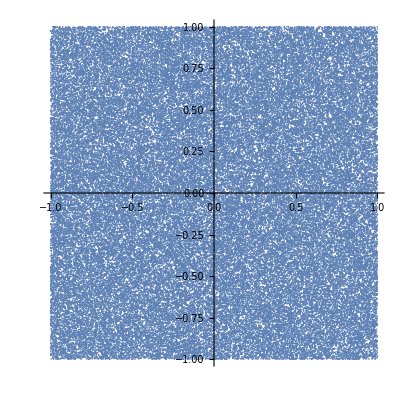

```mathematica
mcPi1Rand=RandomReal[{-1,1},{mcPi1Dim,2}];
ListPlot[mcPi1Rand,AspectRatio->1]
```

```mathematica
mcPi1=4 Count[Map[Norm,mcPi1Rand],_?(#≤1&)]/mcPi1Dim//N
```

3.14496

### Integration Using Pure Random Variables

The function we need to integrate is

```mathematica
mcIntfunc[x_]:=1/(1+Sinh[2*x]*(Log[x])^2);
```

The result, however is

```mathematica
NIntegrate[mcIntfunc[x],{x,0.8,3}]
```

0.67684

The length of the list is

```mathematica
mcInt1N=10;
```

Make up a function that generates a list of variables

```mathematica
mcInt1RV[numberoframdom_]:=Table[Random[Real,{0.8,3}],{i,1,numberoframdom}]
```

The list we need

```mathematica
mcInt1RVList=mcInt1RV[mcInt1N]
```

{1.17137,2.28145,1.07451,1.23374,1.76644,1.1343,2.59571,2.46394,0.941493,1.40329}

```mathematica
mcInt1Result1=(3-0.8)/mcInt1N Total[mcIntfunc[mcInt1RVList]]
```

1.16667

These can be combined to one line

```mathematica
mcInt1[ini_,fin_,number_]:=Module[{listTemp=Table[Random[Real,{ini,fin}],{i,1,number}]},(fin-ini)/number Total[mcIntfunc[listTemp]]]
```

If we do a dim 10 list, we get

```mathematica
mcInt1[0.8,3,10]
```

0.472923

Compared to the NIntegrate value, this is very bad.

The performance becomes much better as we increase the length of the list

```mathematica
Table[mcInt1[0.8,3,list],{list,{100,1000,3000,6000}}]
```

{0.815396,0.651564,0.657192,0.65422}

The standard routine is to do repeat then average

```mathematica
Mean[Table[mcInt1[0.8,3,100],{i,1,100}]]
```

0.687474

For comparision purpose,

```mathematica
mcInt1Mean[number_]:=Mean[Table[mcInt1[0.8,3,number],{i,1,number}]]
```

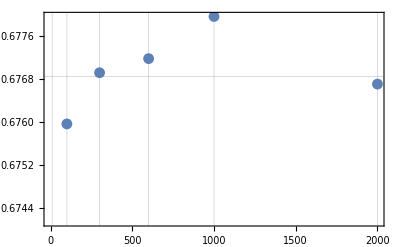

```mathematica
mcInt1MeanList1=Table[{list,mcInt1Mean[list]},{list,{10,100,300,600,1000,2000}}];
ListPlot[%,GridLines->{{10,100,300,600,1000,2000}, {NIntegrate[mcIntfunc[x],{x,0.8,3}]}},Frame->True]
```

### An integration of a function With the help of a Integrable know distribution

https://en.wikipedia.org/wiki/Monte_Carlo_integration#Wolfram_Mathematica_Example

All functions starts with a name mcInt in this part.

Number of random variables

```mathematica
mcIntRVN=100;
```

The function we want to integrate (integrate from 0.8 to 3 over x)

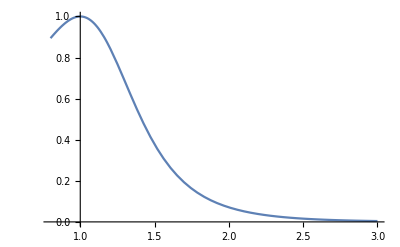

```mathematica
mcIntfunc[x_]:=1/(1+Sinh[2*x]*(Log[x])^2);
mcIntfuncPlt=Plot[mcIntfunc[x],{x,0.8,3}]
```

Find a distribution that we can integrate analytically, like a normal distribution,

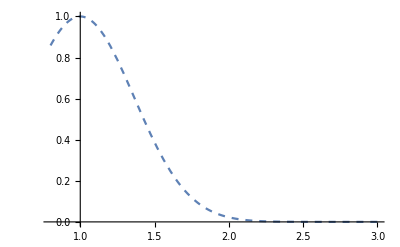

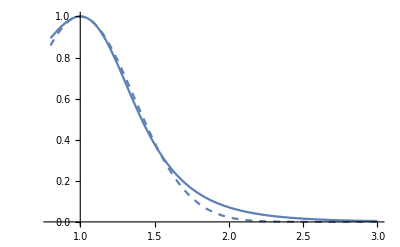

```mathematica
Plot[PDF[NormalDistribution[1,0.399],1.1*x-0.1],{x,0.8,3},PlotStyle->Dashed]
Show[mcIntfuncPlt,%]
```

So this looks quite close to our integrand. We can make some use of it. I am going to make up this distribution for comparision and normalization use.

```mathematica
mcIntDist[x_,average_,var_]:=PDF[NormalDistribution[average,var],1.1*x-0.1];
```

Generate random list/table

```mathematica
mcIntRV[mcIntRVN_]:=RandomVariate[TruncatedDistribution[{0.8,3},NormalDistribution[1,0.399]],mcIntRVN];
```

The ratio func[RV]/Distrib[RV, 1, 0.399] is ratio of our integrand and standard distribution. We just total everything then normalize it.

```mathematica
mcIntRVList=mcIntRV[mcIntRVN]
```

{0.802886,1.22497,1.88417,1.0066,1.57752,1.20244,1.28128,0.820047,1.31415,1.53412,0.880593,1.14707,0.945326,1.74111,1.4593,0.82673,1.52239,0.870111,0.820183,1.22869,0.814949,1.22961,1.60759,1.37952,1.26759,1.15618,1.11942,1.09244,1.45684,0.814849,1.04667,1.01056,1.16428,1.0486,1.22838,1.40626,0.998072,1.58531,0.943805,1.22533,1.14828,1.1599,0.997718,1.46089,1.12283,1.08617,1.34671,1.42876,1.11829,0.85638,0.920348,1.30668,1.36329,0.993597,0.843274,1.23556,1.23173,1.15802,1.18579,0.852243,1.42217,1.28129,1.5301,1.13511,1.53415,1.40801,1.04807,1.2299,1.00159,0.960653,1.21345,1.19984,0.8163,1.46419,0.936768,1.34482,1.36359,1.16215,1.61938,1.02245,1.01967,1.2668,1.4649,1.04802,1.02149,1.19023,1.67145,1.48385,1.29132,0.846579,0.930907,1.48969,1.04505,1.95813,1.21072,1.08827,1.3246,1.14966,1.48306,1.04393}

```mathematica
mcIntResult=1/mcIntRVN Total[mcIntfunc[mcIntRVList]/mcIntDist[mcIntRVList,1,0.399]]*Integrate[mcIntDist[x,1,0.399],{x,0.8,3}]
```

0.660599

As a verification, we calculate the integrate using the NIntegrate[] function,

```mathematica
NIntegrate[mcIntfunc[x],{x,0.8,3}]
```

0.67684

Actually we can just make it one line,

```mathematica
mcIntG[mcIntRVN_]:=Module[{listTemp=RandomVariate[TruncatedDistribution[{0.8,3},NormalDistribution[1,0.399]],mcIntRVN]},1/mcIntRVN Total[mcIntfunc[listTemp]/mcIntDist[listTemp,1,0.399]]*Integrate[mcIntDist[x,1,0.399],{x,0.8,3}]]
```

```mathematica
mcIntG[1000]
```

0.694088

It is very important to realize that we need to use the same listTemp or mcIntRVList in one calculation!!!!

To see how well this works, Take the mcIntRVList to be 100 dim, run 100 times then average the results.

```mathematica
Mean[Table[mcIntG[100],{i,1,100}]]
```

0.737143

```mathematica
Mean[Table[mcIntG[100],{i,1,1000}]]
```

0.794299

```mathematica
(* Can also plot a list:
ListPlot[Table[Mean[Table[mcIntG[100],{i,1,j}]],{j,100,1000,100}]]
*)
```

$Aborted

```mathematica
NIntegrate[mcIntfunc[x],{x,0.8,3}]
```